La funzione da calcolare è:

x-√(-1+x^2)

----------------------------------------------------------------------------------------

I contenuti sotto radice pari

{-1+x^2}

devono essere maggiori di zero:

{x<-1||x>1}

I contenuti sotto logaritmi

{}

devono essere maggiori di zero:

{}

Il denominatore:

{1}

deve essere diverso di zero, quindi calcolo i valori per cui il denominatore è minore di zero e maggiore di zero e risulta:

{False,True}

quindi facendo l'intersezione tra questi domini, il dominio è:

x≤-1||x≥1

----------------------------------------------------------------------------------------

La funzione non è pari.

La funzione non è dispari.

----------------------------------------------------------------------------------------

Per scoprire dove interseca l'asse x poniamo il numeratore = 0:

x-√(-1+x^2)==0

che risulta:

falso, non esistono intersezioni con l'asse x.

Per scoprire dove interseca l'asse y, calcoliamo f(x) con x=0 se il dominio lo ammette e otteniamo che interseca l'asse y in

y==-ⅈ

----------------------------------------------------------------------------------------

La funzione è positiva per x≥1

----------------------------------------------------------------------------------------

Gli estremi inferiori per il calcolo del limite sono:

{1}

e gli estremi superiori sono:

{-1}

Il limite per x->-∞ nell'intorno destro = -∞ quindi è un asintoto verticale.

Il limite per x->∞ nell'intorno sinistro = 0 quindi è un asintoto orizzontale.

Il limite per x->1 nell'intorno destro = 1 quindi è un asintoto orizzontale.

Il limite per x->-1 nell'intorno sinistro = -1 quindi è un asintoto orizzontale.

----------------------------------------------------------------------------------------

La derivata prima della funzione è:

1-x/(√(-1+x^2))

Non ci sono soluzioni per la derivata prima.

Gli intervalli in cui la derivata è positiva sono:

x<-1.

Gli intervalli in cui la derivata è negativa sono:

x>1.

Il grafico della derivata prima è il seguente:

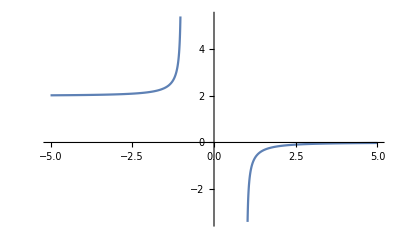

----------------------------------------------------------------------------------------

La derivata seconda è

x^2/((-1+x^2)^(3/2))-1/(√(-1+x^2))

Non ci sono soluzioni per la derivata prima.

Il grafico della derivata seconda è il seguente:

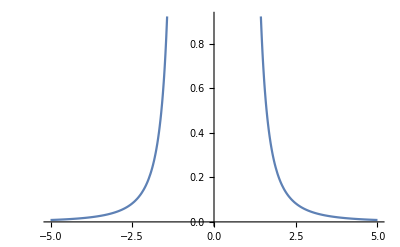

----------------------------------------------------------------------------------------

Il grafico della funzione è:

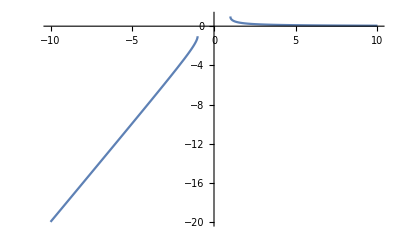

```mathematica
$IterationLimit=$RecursionLimit=50;

Get["Desktop/Progetto Matematica Computazionale/studiofunzioni.m"]

Print["La funzione da calcolare è: "]
f[x_]:=x-Sqrt[x^2-1];
f[x]
(*(E^x-1)/x
x^3 
(E^x-1)/x
x-Sqrt[x^2-1]
(Sqrt[3]-2*x-Log[35])/(2*x)
(2*x-1)/(x*E^x)
(x*(x-1)^2)/(x+1)^2
x/(E^x-1)
x^2/2-x+Log[x+1]
*)

Print["----------------------------------------------------------------------------------------"];

CalcolaDominio[f,x]

Print["----------------------------------------------------------------------------------------"];

ControlloPariDispari[f,x]

Print["----------------------------------------------------------------------------------------"];

ControlloIntersezioneAssi[f,x]

Print["----------------------------------------------------------------------------------------"];

SegnoFunzione[f,x]

Print["----------------------------------------------------------------------------------------"];

CalcolaLimiti[f,x]

Print["----------------------------------------------------------------------------------------"];

SegnoDerivataPrima[f,x]

Print["----------------------------------------------------------------------------------------"];

SegnoDerivataSeconda[f,x]

Print["----------------------------------------------------------------------------------------"];

GraficoFunzione[f,x]
```